```mathematica
SetDirectory["/home/lina/Documents/SimulacionesTesis/resultados3/v2/data"];
```

```mathematica
(*data1=Map[Partition[#,30]&,ToExpression@Import["OneGenR_0.6","CSV"]][[All,All,1;;25]];*)
```

```mathematica
(*Export["OneGenR_0.5",Map[Partition[Flatten[#,2],2]&,data1],"CSV"]*)
```

## Individual graphs

## GA

### Escalas características

```mathematica
data=ToExpression@Table[Import["controlAIGAI_I_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["controlAIGAI_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
(****************************************************)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
(****************************************************)
modelo="controlGA, Act-Inh I_I ";
```

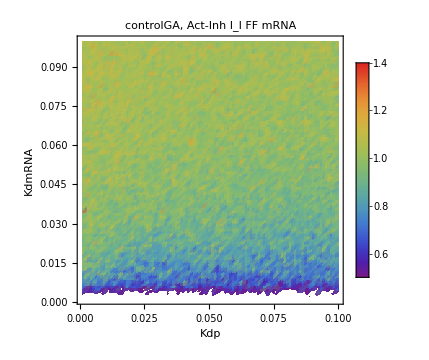
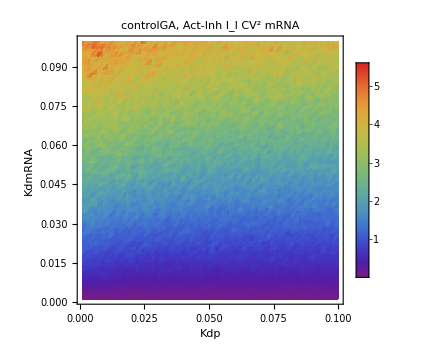
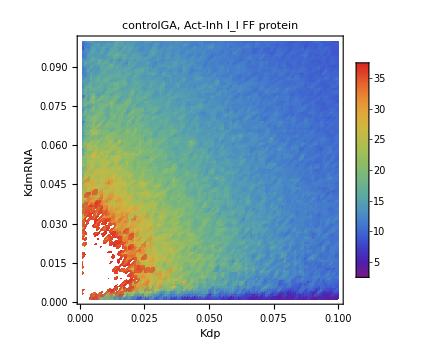
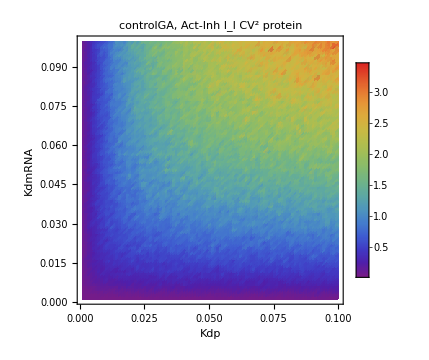

```mathematica
(****************************************************)Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA"},{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA"},{ffProtein,ToString[modelo]<>" \n  FF protein"},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein"}}}]
```

## burstmRNA

```mathematica
data=ToExpression@Table[Import["burstmRCLE_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["burstmRCLE_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
data=ToExpression@Table[Import["burstmAICLEInh_I_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data=ToExpression@Table[Import["burstmAICLEInh_I_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
data=ToExpression@Table[Import["burstmAICLEAct_I_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2."}}];
```

```mathematica
data=ToExpression@Table[Import["burstmAICLEAct_A_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
(****************************************************)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
(****************************************************)
```

```mathematica
modelo="burstmRNA, One G R CLE";
```

```mathematica
modelo="burstmRNA, Act-Inh_A_A, CLE";
```

```mathematica
modelo="burstmRNA, Act-Inh_A_I, CLE";
```

```mathematica
modelo="burstmRNA, Act-Inh_I_A, CLE";
```

```mathematica
modelo="burstmRNA, Act-Inh_I_I, CLE";
```

```mathematica
modelo="Act-Inh_A_, GA";
```

```mathematica
modelo="Act-Inh_I_I, GA";
```

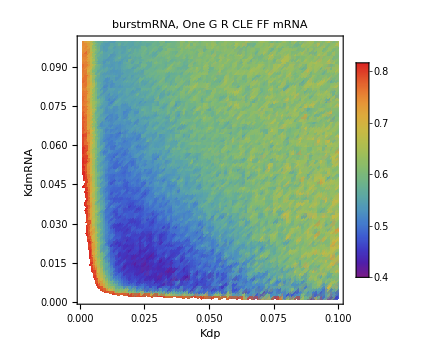
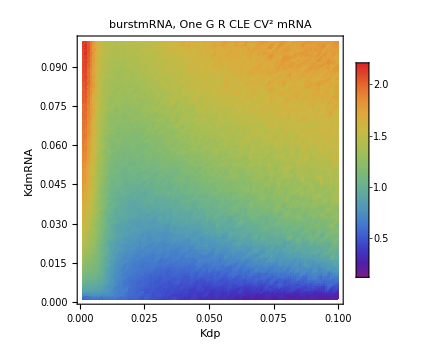
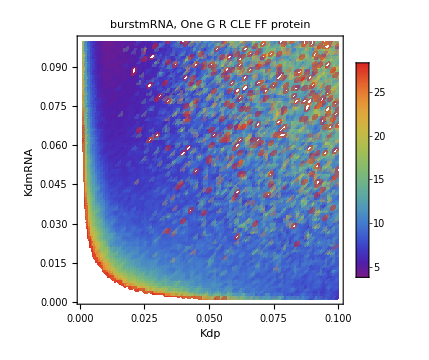
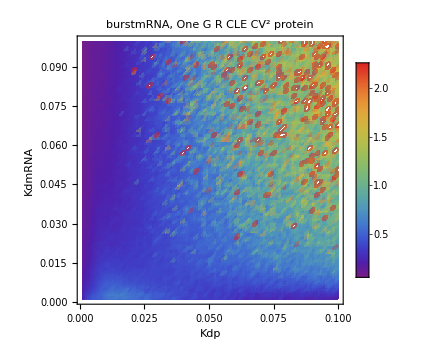

```mathematica
(****************************************************)Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA,ToString[modelo]<>" \n FF mRNA"},{cv2mRNA,ToString[modelo]<>" \n  CV^2 mRNA"},{ffProtein,ToString[modelo]<>" \n  FF protein"},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein"}}}]
```

## bothBurst

```mathematica
(*{"0.025","0.05","0.075","0.1"}{"0.5","1.","1.5","2"} *)
```

```mathematica
data2=ToExpression@Table[Import["bothBRCLE2γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1,All,1]][[All,All,1]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1,All,1]][[All,All,2]]]]];
```

```mathematica
(*OneGen*)
modelo="CLE";Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->(*{"Koff","Kon"}*){"KdmRNA","Koff"}(*{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.02,2}(*{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein,"BothB One Gen R "<>ToString[modelo]<>" \n  FF protein"},{cv2Protein,"BothB One Gen R "<>ToString[modelo]<>" \n  CV^2 protein"}}}]
```

## burstProtein

```mathematica
data=Map[Flatten[#,1]&,ToExpression@Table[Import["burstPRCLE_γg"<>i,"CSV"],{i,{"1.5","2"}}]];
```

```mathematica
data=Map[Flatten[#,1]&,ToExpression@Table[Import["burstPRCLE_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}]];
```

```mathematica
(****************************************************)
ffProtein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,25]&,data[[All,All,2(*cv2*)]]]]];
```

```mathematica
(****************************************************)
```

```mathematica
modelo="burstP, One G R CLE";
```

```mathematica
modelo="burstP, Act-Inh_A_A, CLE";
```

```mathematica
modelo="burstP, Act-Inh_A_I, CLE";
```

```mathematica
modelo="burstP, Act-Inh_I_A, CLE";
```

```mathematica
modelo="burstP, Act-Inh_I_I, CLE";
```

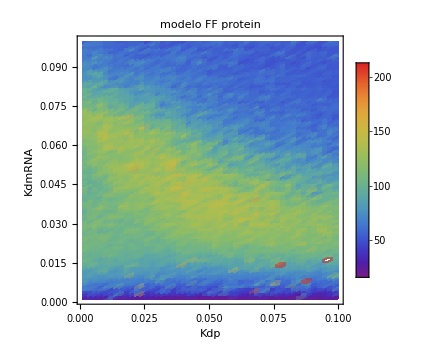
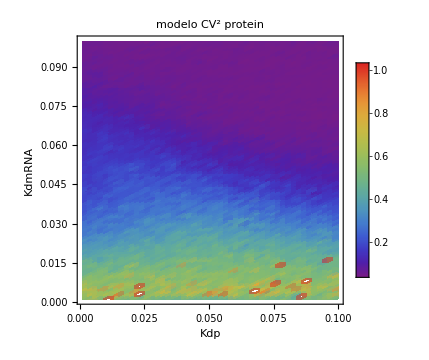

```mathematica
(****************************************************)Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein,ToString[modelo]<>" \n  FF protein"},{cv2Protein,ToString[modelo]<>" \n  CV^2 protein"}}}]
```

## Comparison

## Data processing

### Funciones

```mathematica
JSDDivergence[data1_,data2_,delta_,quantile_List]:=Module[{data1cut,data2cut,range,pList,qList,mList,divergence},
data1cut=Select[Flatten[data1],Quantile[Flatten[data1],quantile][[1]]<#<Quantile[Flatten[data1],quantile][[2]]&];
data2cut=Select[Flatten[data2],Quantile[Flatten[data2],quantile][[1]]<#<Quantile[Flatten[data2],quantile][[2]]&];
range={Min[Flatten[{data1cut,data2cut}]],Max[Flatten[{data1cut,data2cut}]]};
{pList,qList}=Transpose@Table[{PDF[HistogramDistribution[data1cut],x],PDF[HistogramDistribution[data2cut],x]},{x,Range[Sequence@@range,delta]}];
mList=(pList+qList)/2;
divergence=1/2 Total@DeleteCases[Table[pList[[i]]*Log[pList[[i]]/(mList[[i]]+0.000001)],{i,1,Length[pList]}],Indeterminate]+1/2 Total@DeleteCases[Table[qList[[i]]*Log[qList[[i]]/(mList[[i]]+0.000001)],{i,1,Length[qList]}],Indeterminate]](* Cuando aparecen errores de indeterminación es porque las curvas no se solapan en ningun punto*)
```

```mathematica
histograma[label_,plotlabel_,color_,data_List,quantile_List]:=Histogram[Select[Flatten[data],Quantile[Flatten[data],quantile][[1]]<#<Quantile[Flatten[data],quantile][[2]]&],"Sturges","Probability",Frame->True,FrameLabel->label,PlotLabel-> plotlabel,ImageSize-> Small,ChartStyle->color]
```

```mathematica
ttest[data_List]:=Table[TTest[{data[[i]],data[[j]]},0,"PValue"],{i,Length[data]},{j,Length[data]}]//MatrixForm
```

```mathematica
MWtest[data_List,quantile_List]:=Module[{data2},
data2=Table[Select[Flatten[i],Quantile[Flatten[i],quantile][[1]]<#<Quantile[Flatten[i],quantile][[2]]&],{i,data}];Table[MannWhitneyTest[{data2[[i]],data2[[j]]},0,"PValue"],{i,Length[data2]},{j,Length[data2]}]//MatrixForm]
```

## comparing methodology with OneGenR

### Uploading data

```mathematica
data1=ToExpression@Table[Import["controlRGA_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
data2=ToExpression@Table[Import["burstmRCLE_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
data3=Map[Flatten[#,1]&,ToExpression@Table[Import["burstPRCLE_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}]];
data4=ToExpression@Table[Import["bothBRCLE_γg"<>i,"CSV"],{i,{"0.5","1","1.5","2"}}];
```

```mathematica
data1=ToExpression@Table[Import["controlRGA_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data2=ToExpression@Table[Import["burstmRCLE_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data3=Map[Flatten[#,1]&,ToExpression@Table[Import["burstPRCLE_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}]];
data4=ToExpression@Table[Import["bothBRCLE_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
(****************************************************)
```

```mathematica
ffmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,All,1(*FF*)]]]]];
cv2Protein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,All,2(*cv2*)]]]]];
```

```mathematica
ffProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1,All,1]][[All,All,1]]]]];
cv2Protein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1,All,1]][[All,All,2]]]]];
```

### Kdp-KdmRNA One Gene Regulated

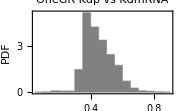
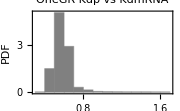

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

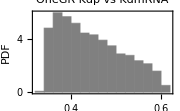
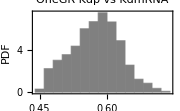

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

(-8.99967×10^-6 | 2.71663
2.71663 | -0.0000119997)

(-3.×10^-6 | 3.29245
3.29245 | -3.×10^-6)

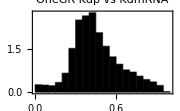
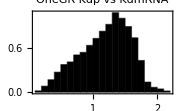

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,CLE","PDF"},Flatten@cv2mRNA2}}}]
```

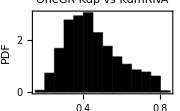
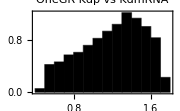

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-9.99999×10^-6 | 4.18384
4.18384 | -0.0000209999)

(-6.99999×10^-6 | 5.35656
5.35656 | -0.000013)

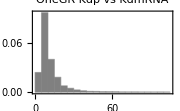
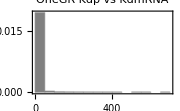
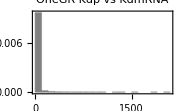
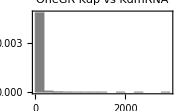

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein,bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

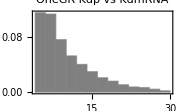
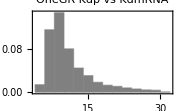
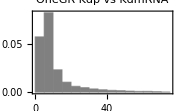
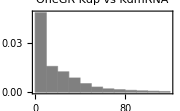

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-9.98752×10^-7 | 0.0000635494 | 0.0263166 | 0.0263519
0.0000635494 | -1.98517×10^-6 | 0.0270557 | 0.0262199
0.0263166 | 0.0270557 | -4.97396×10^-6 | 0.0261083
0.0263519 | 0.0262199 | 0.0261083 | -6.91777×10^-6)

(-0.0000249991 | 0.0714798 | 0.0911332 | 0.256095
0.0714798 | -0.0000249989 | 0.195876 | 0.302495
0.0911332 | 0.195876 | -0.0000669809 | 0.152783
0.256095 | 0.302495 | 0.152783 | -0.000115963)

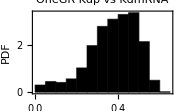
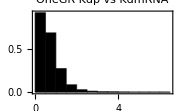
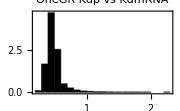
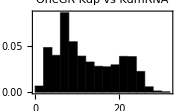

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein,bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

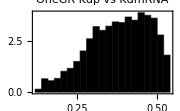
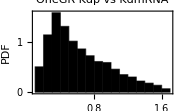
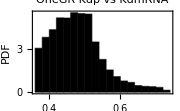
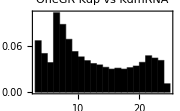

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-6.99997×10^-6 | 2.23362 | 1.47526 | 6.99644
2.23362 | -0.000049991 | 2.36819 | 6.4485
1.47526 | 2.36819 | -0.0000179989 | 6.78173
6.99644 | 6.4485 | 6.78173 | -0.000307955)

(-5.×10^-6 | 2.06107 | 1.96836 | 6.80867
2.06107 | -0.000016 | 2.87886 | 6.72701
1.96836 | 2.87886 | -4.×10^-6 | 7.12255
6.80867 | 6.72701 | 7.12255 | -0.000209997)

### KdmRNA-Koff One Gene Regulated

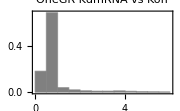
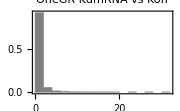

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

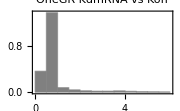
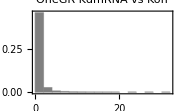

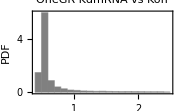
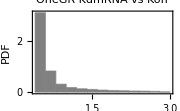

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
({{-0.00005699795766267894, 0.4041579589230816}, {0.4041579589230816, -0.00009798947251878121}})
```

(-0.0000199999 | 1.01369
1.01369 | -0.0000239998)

```mathematica
MWtest[{ffmRNA1,ffmRNA2},{0.05,0.95}]
```

(0.999999 | 6.24217×10^-182
6.24268×10^-182 | 0.999999)

```mathematica
({{0.9999990225261791, 3.8448253568456856*^-133}, {3.8450570633497445*^-133, 0.9999990225261791}})
```

```mathematica
({{0.9999990228194018, 4.514939936598919*^-133}, {4.515211873467762*^-133, 0.9999990228194018}})
```

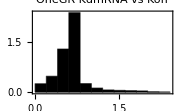
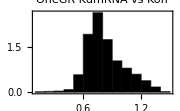

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,CLE","PDF"},Flatten@cv2mRNA2}}}]
```

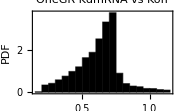
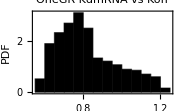

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-0.0000229994 | 1.58755
1.58755 | -0.0000139999)

```mathematica
({{-9.999956113135698*^-6, 1.8216721529062845}, {1.8216721529062845, -6.99999685873734*^-6}})
```

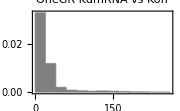
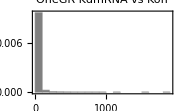
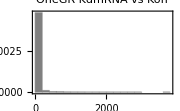
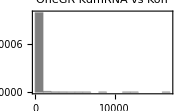

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein, bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

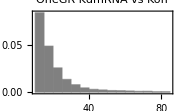
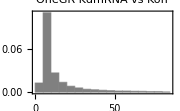
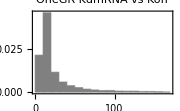
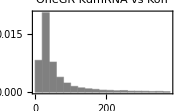

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-2.99254×10^-6 | 0.053606 | 0.017001 | 0.00394853
0.053606 | -1.999×10^-6 | 0.0537708 | 0.00382007
0.017001 | 0.0537708 | -0.0000108525 | 0.00360347
0.00394853 | 0.00382007 | 0.00360347 | -0.0000259027)

```mathematica
({{-0.00007197954398908529, 0.2993899188801601, 0.11008199705967009, 0.1939729160386217}, {0.2993899188801601, -0.00007798156726603881, 0.1969109042746248, 0.3566430021371841}, {0.11008199705967009, 0.1969109042746248, -0.00015490894157899326, 0.18946423356439052}, {0.1939729160386217, 0.3566430021371841, 0.18946423356439052, -0.00036854933449073407}})
```

```mathematica
MWtest[{ffProtein1,ffProtein2,ffProtein3,ffProtein4},{0.05,0.95}]
```

(0.999999 | 0. | 6.78519×10^-87 | 0.
0. | 0.999999 | 0. | 0.
6.7848×10^-87 | 0. | 0.999999 | 0.
0. | 0. | 0. | 0.999999)

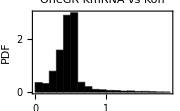
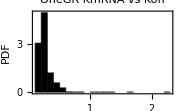
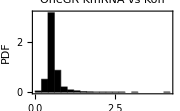
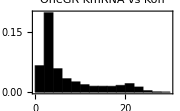

```mathematica
Table[histograma[i[[1]],"OneGR KmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein, bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

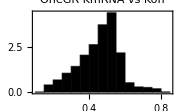
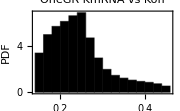
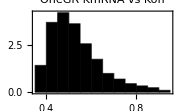
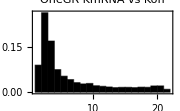

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-0.0000189996 | 2.79598 | 0.628982 | 6.65374
2.79598 | -9.99958×10^-6 | 3.90708 | 6.41625
0.628982 | 3.90708 | -0.0000209989 | 6.66747
6.65374 | 6.41625 | 6.66747 | -0.000272959)

(-6.99999×10^-6 | 4.0067 | 0.941347 | 7.15371
4.0067 | -4.×10^-6 | 6.04897 | 7.48107
0.941347 | 6.04897 | -6.×10^-6 | 6.84946
7.15371 | 7.48107 | 6.84946 | -0.000196996)

### Koff-Kon One Gene Regulated

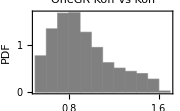
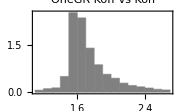

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0.05,0.95}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

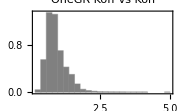
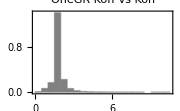

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
({{-0.00010999918695432057, 5.838195262606714}, {5.838195262606714, -0.0001599953611507452}})
```

```mathematica
({{-0.00003799584324223993, 3.9452712777162353}, {3.9452712777162353, -0.00008097833252158497}})
```

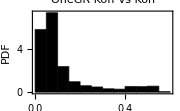
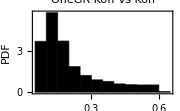

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Black,i[[2]],{0.05,0.95}],{i,{{{"CV2 mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"CV2 mRNA,burstmCLE","PDF"},Flatten@cv2mRNA2}}}]
```

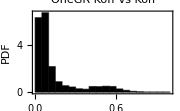
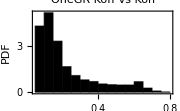

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

```mathematica
({{-0.00005999954788806183, 3.9969560398231003}, {3.9969560398231003, -0.0000599996625615129}})
```

(-8.99994×10^-6 | 1.24134
1.24134 | -7.99991×10^-6)

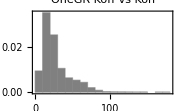
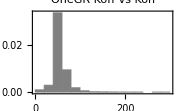
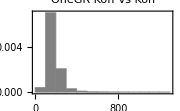

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein, bothBCLE2CLE","PDF"},Flatten@ffProtein4}}}]
```

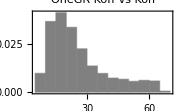
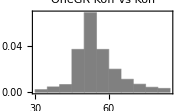
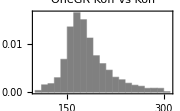

```mathematica
Table[JSDDivergence[i,j,1,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein4}}]//MatrixForm
```

```mathematica
({{-0.00014747957513137745, 0.3335968510642072, 0.6410197340942566}, {0.3335968510642072, -0.00023639786011133416, 0.5873943468970071}, {0.6410197340942566, 0.5873943468970071, -0.0009989445852557038}})
```

```mathematica
({{-0.000579707069194458, 0.4510356825075909, 0.6902528814149005}, {0.4510356825075909, -0.0005296126649052828, 0.6888226983559401}, {0.6902528814149005, 0.6888226983559401, -0.0019442654290775497}})
```

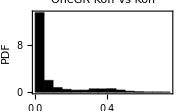
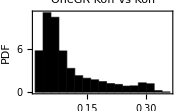
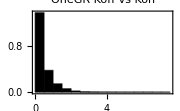

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein, bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

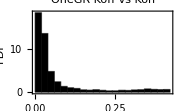
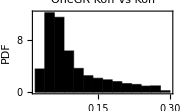
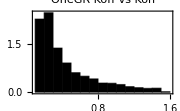

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein4}}]//MatrixForm
```

(-7.99986×10^-6 | 7.58529 | 8.2274
7.58529 | -4.×10^-6 | 2.34369
8.2274 | 2.34369 | -0.0000509952)

```mathematica
({{-4.999996739017614*^-6, 5.7781767420376, 6.50166012360857}, {5.7781767420376, -2.9999992785846943*^-6, 4.645220940355409}, {6.50166012360857, 4.645220940355409, -0.000013999974987104953}})
```

## comparing algorithms- same scale

```mathematica
(****************************************************)
modelo1="controlGA, One R G ";
modelo2="burstmRNA, One R G ";
modelo3="burstP, One R G ";
modelo4="bothBurst, One R G ";
```

```mathematica
ffmRNA2[[1,1]]=0.1;
```

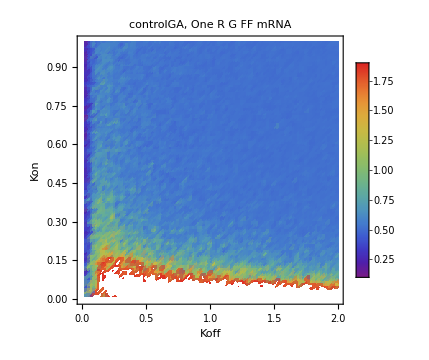
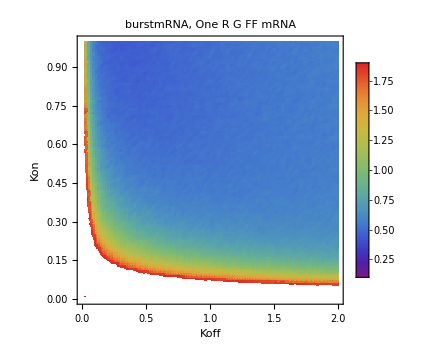

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {0.1,1.9},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA1,ToString[modelo1]<>" \n FF mRNA"},{ffmRNA2,ToString[modelo2]<>" \n FF mRNA"}}}]
```

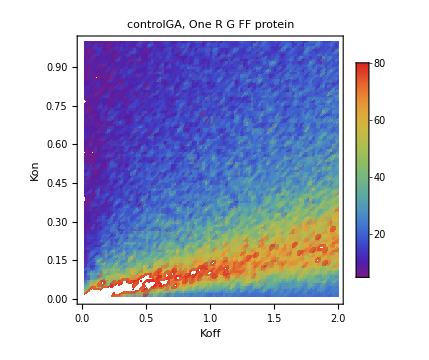
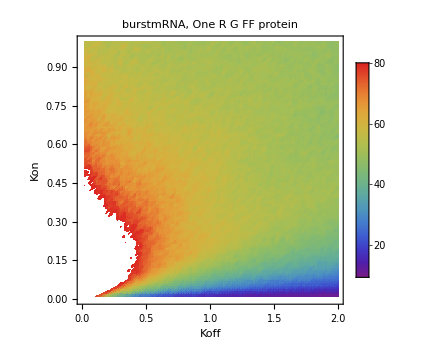
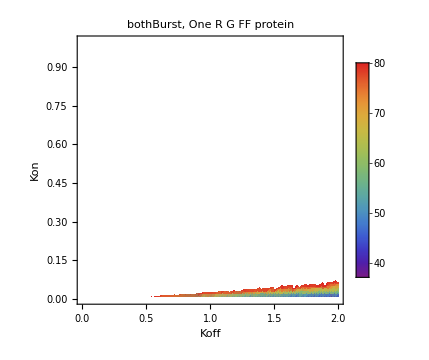

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {5,80},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein1,ToString[modelo1]<>" \n FF protein"},{ffProtein2,ToString[modelo2]<>" \n FF protein"}(*,{ffProtein3,ToString[modelo3]<>" \n FF protein"}*),{ffProtein4,ToString[modelo4]<>" \n FF protein"}}}]
```

## Comparing sub-circuits with GA

### Uploading data

```mathematica
(****NOTA IMPORTANTE!!!!!: Cuando tenga lista todos los de GA se hacen estas graficas con la misma escala para todas y poder comparar entre estas. Por el momento solo voy a revisar las que tengo*)
```

```mathematica
SetDirectory["/home/lina/Documents/SimulacionesTesis/resultados3/v2/data"];
```

```mathematica
data0=ToExpression@Table[Import["controlConstGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];ffmRNA0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein0=Map[Flatten,Transpose[Map[Partition[#,25]&,data0[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
data1=ToExpression@Table[Import["controlUnRGA_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
data2=ToExpression@Table[Import["controlRGA_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
data3=ToExpression@Table[Import["controlAIGAA_A_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
data4=ToExpression@Table[Import["controlAIGAA_I_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];data5=ToExpression@Table[Import["controlAIGAI_A_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
data6=ToExpression@Table[Import["controlAIGAI_I_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data1=ToExpression@Table[Import["controlUnRGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data2=ToExpression@Table[Import["controlRGA_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data3=ToExpression@Table[Import["controlAIGAA_A_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data4=ToExpression@Table[Import["controlAIGAA_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data5=ToExpression@Table[Import["controlAIGAI_A_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
data6=ToExpression@Table[Import["controlAIGAI_I_γp"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

#### (****************************************************)

```mathematica
ffmRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein1=Map[Flatten,Transpose[Map[Partition[#,25]&,data1[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein3=Map[Flatten,Transpose[Map[Partition[#,25]&,data3[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein4=Map[Flatten,Transpose[Map[Partition[#,25]&,data4[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein5=Map[Flatten,Transpose[Map[Partition[#,25]&,data5[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
ffmRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein6=Map[Flatten,Transpose[Map[Partition[#,25]&,data6[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

### Koff-Kon Histogram

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@ffmRNA1},{{"FF mRNA,RG","PDF"},Flatten@ffmRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@ffmRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@ffmRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@ffmRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@ffmRNA6}}}]
```

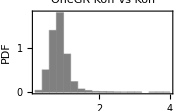
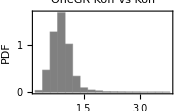
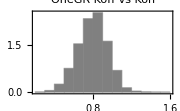
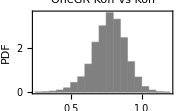
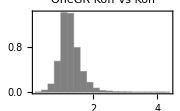
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
MWtest[dat]
```

(0.999999 | 1.44227×10^-15 | 4.48146×10^-15 | 2.62479×10^-122 | 6.51501×10^-266 | 0.
1.44229×10^-15 | 0.999999 | 0.14452 | 4.63114×10^-163 | 3.31786×10^-276 | 0.
4.48154×10^-15 | 0.144519 | 0.999999 | 2.95276×10^-216 | 0. | 0.
2.62464×10^-122 | 4.63083×10^-163 | 2.95253×10^-216 | 0.999999 | 5.21313×10^-39 | 0.
6.51445×10^-266 | 3.31757×10^-276 | 0. | 5.21297×10^-39 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

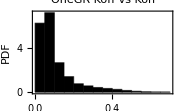
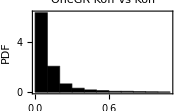
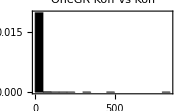
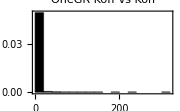
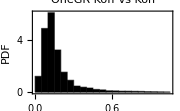
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Black,i[[2]],{0,1}],{i,{{{"CV2 mRNA,UnRG","PDF"},Flatten@cv2mRNA1},{{"CV2 mRNA,RG","PDF"},Flatten@cv2mRNA2},{{"CV2 mRNA,AI_A_A","PDF"},Flatten@cv2mRNA3},{{"CV2 mRNA,AI_A_I","PDF"},Flatten@cv2mRNA4},{{"CV2 mRNA,AI_I_A","PDF"},Flatten@cv2mRNA5},{{"CV2 mRNA,AI_I_I","PDF"},Flatten@cv2mRNA6}}}]
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}},{j,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}}]//MatrixForm
```

(-4.×10^-6 | 0.450124 | 0.00733976 | 7.93636 | 7.93249 | 3.79239
0.450124 | -6.×10^-6 | 0.471236 | 8.15588 | 8.15201 | 4.27185
0.00733976 | 0.471236 | -4.×10^-6 | 7.82275 | 7.81888 | 3.53378
7.93636 | 8.15588 | 7.82275 | -0.0000849981 | 0.211934 | 6.70782
7.93249 | 8.15201 | 7.81888 | 0.211934 | -0.0000719989 | 6.70394
3.79239 | 4.27185 | 3.53378 | 6.70782 | 6.70394 | -4.99999×10^-6)

```mathematica
MWtest[Map[Flatten,{cv2mRNA1,cv2mRNA2,cv2mRNA3,cv2mRNA4,cv2mRNA5,cv2mRNA6}]]
```

(0.999999 | 9.44908×10^-8 | 8.46131×10^-8 | 0. | 0. | 0.
9.44921×10^-8 | 0.999999 | 0.971874 | 0. | 0. | 0.
8.46143×10^-8 | 0.971876 | 0.999999 | 0. | 0. | 0.
0. | 0. | 0. | 0.999999 | 1.63831×10^-64 | 0.
0. | 0. | 0. | 1.63837×10^-64 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

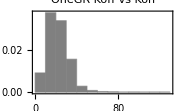
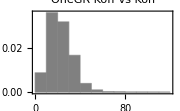
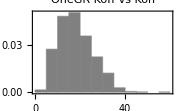
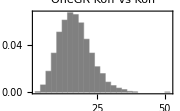
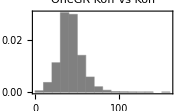
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[histograma[i[[1]],"OneGR Koff vs Kon ",Gray,i[[2]],{0,1}],{i,{{{"FF protein,UnRG","PDF"},Flatten@ffProtein1},{{"FF protein,RG","PDF"},Flatten@ffProtein2},{{"FF protein,AI_A_A","PDF"},Flatten@ffProtein3},{{"FF protein,AI_A_I","PDF"},Flatten@ffProtein4},{{"FF protein,AI_I_A","PDF"},Flatten@ffProtein5},{{"FF protein,AI_I_I","PDF"},Flatten@ffProtein6}}}]
```

```mathematica
Table[JSDDivergence[i,j,5,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}}]//MatrixForm
```

$Aborted

```mathematica
MWtest[Map[Flatten,{ffProtein1,ffProtein2,ffProtein3,ffProtein4,ffProtein5,ffProtein6}]]
```

(0.999999 | 2.02571×10^-28 | 0.000724421 | 7.25567×10^-175 | 0. | 0.
2.02577×10^-28 | 0.999999 | 5.8749×10^-17 | 1.39072×10^-261 | 0. | 0.
0.000724427 | 5.87478×10^-17 | 0.999999 | 1.05703×10^-212 | 0. | 0.
7.25517×10^-175 | 1.39061×10^-261 | 1.05694×10^-212 | 0.999999 | 1.75489×10^-22 | 0.
0. | 0. | 0. | 1.75485×10^-22 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

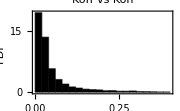
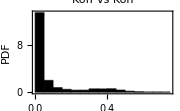
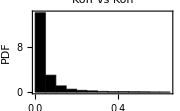
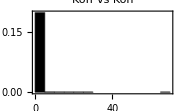
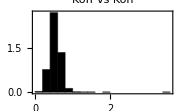
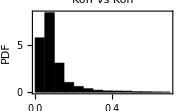

```mathematica
Table[histograma[i[[1]]," Koff vs Kon ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,UnRG","PDF"},Flatten@cv2Protein1},{{"CV2 protein,RG","PDF"},Flatten@cv2Protein2},{{"CV2 protein,AI_A_A","PDF"},Flatten@cv2Protein3},{{"CV2 protein,AI_A_I","PDF"},Flatten@cv2Protein4},{{"CV2 mRNA,AI_I_A","PDF"},Flatten@cv2Protein5},{{"CV2 protein,AI_I_I","PDF"},Flatten@cv2Protein6}}}]
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}}]//MatrixForm
```

(-7.99986×10^-6 | 7.58529 | 8.2274
7.58529 | -4.×10^-6 | 2.34369
8.2274 | 2.34369 | -0.0000509952)

```mathematica
MWtest[Map[Flatten,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4,cv2Protein5,cv2Protein6}]]
```

(0.999999 | 5.83608×10^-13 | 0.000107471 | 0. | 0. | 0.
5.83619×10^-13 | 0.999999 | 0.000610754 | 0. | 0. | 0.
0.000107472 | 0.000610748 | 0.999999 | 0. | 0. | 0.
0. | 0. | 0. | 0.999999 | 1.40456×10^-52 | 0.
0. | 0. | 0. | 1.40451×10^-52 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

### KdmRNA-Koff Histogram

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@ffmRNA1},{{"FF mRNA,burstmCLE","PDF"},Flatten@ffmRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0.05,0.95}],{i,{ffmRNA1,ffmRNA2}},{j,{ffmRNA1,ffmRNA2}}]//MatrixForm
```

```mathematica
({{-0.00005699795766267894, 0.4041579589230816}, {0.4041579589230816, -0.00009798947251878121}})
```

(-0.0000199999 | 1.01369
1.01369 | -0.0000239998)

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,GA","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,CLE","PDF"},Flatten@cv2mRNA2}}}]
```

{-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-0.0000229994 | 1.58755
1.58755 | -0.0000139999)

```mathematica
({{-9.999956113135698*^-6, 1.8216721529062845}, {1.8216721529062845, -6.99999685873734*^-6}})
```

```mathematica
Table[histograma[i[[1]],"OneGR KdmRNA vs Koff",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein, bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-2.99254×10^-6 | 0.053606 | 0.017001 | 0.00394853
0.053606 | -1.999×10^-6 | 0.0537708 | 0.00382007
0.017001 | 0.0537708 | -0.0000108525 | 0.00360347
0.00394853 | 0.00382007 | 0.00360347 | -0.0000259027)

```mathematica
({{-0.00007197954398908529, 0.2993899188801601, 0.11008199705967009, 0.1939729160386217}, {0.2993899188801601, -0.00007798156726603881, 0.1969109042746248, 0.3566430021371841}, {0.11008199705967009, 0.1969109042746248, -0.00015490894157899326, 0.18946423356439052}, {0.1939729160386217, 0.3566430021371841, 0.18946423356439052, -0.00036854933449073407}})
```

```mathematica
Table[histograma[i[[1]],"OneGR KmRNA vs Koff ",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein, bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-0.0000189996 | 2.79598 | 0.628982 | 6.65374
2.79598 | -9.99958×10^-6 | 3.90708 | 6.41625
0.628982 | 3.90708 | -0.0000209989 | 6.66747
6.65374 | 6.41625 | 6.66747 | -0.000272959)

(-6.99999×10^-6 | 4.0067 | 0.941347 | 7.15371
4.0067 | -4.×10^-6 | 6.04897 | 7.48107
0.941347 | 6.04897 | -6.×10^-6 | 6.84946
7.15371 | 7.48107 | 6.84946 | -0.000196996)

### Kdp-KdmRNA Histogram

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA ",Gray,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@ffmRNA1},{{"FF mRNA,RG","PDF"},Flatten@ffmRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@ffmRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@ffmRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@ffmRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@ffmRNA6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{ffmRNA1,ffmRNA2,ffmRNA3,ffmRNA4,ffmRNA5,ffmRNA6}},{j,{ffmRNA1,ffmRNA2,ffmRNA3,ffmRNA4,ffmRNA5,ffmRNA6}}]//MatrixForm
```

$Aborted

```mathematica
MWtest[dat]
```

(0.999999 | 1.44227×10^-15 | 4.48146×10^-15 | 2.62479×10^-122 | 6.51501×10^-266 | 0.
1.44229×10^-15 | 0.999999 | 0.14452 | 4.63114×10^-163 | 3.31786×10^-276 | 0.
4.48154×10^-15 | 0.144519 | 0.999999 | 2.95276×10^-216 | 0. | 0.
2.62464×10^-122 | 4.63083×10^-163 | 2.95253×10^-216 | 0.999999 | 5.21313×10^-39 | 0.
6.51445×10^-266 | 3.31757×10^-276 | 0. | 5.21297×10^-39 | 0.999999 | 0.
0. | 0. | 0. | 0. | 0. | 0.999999)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"FF mRNA,UnRG","PDF"},Flatten@cv2mRNA1},{{"FF mRNA,RG","PDF"},Flatten@cv2mRNA2},{{"FF mRNA,AI_A_A","PDF"},Flatten@cv2mRNA3},{{"FF mRNA,AI_A_I","PDF"},Flatten@cv2mRNA4},{{"FF mRNA,AI_I_A","PDF"},Flatten@cv2mRNA5},{{"FF mRNA,AI_I_I","PDF"},Flatten@cv2mRNA6}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2mRNA1,cv2mRNA2}},{j,{cv2mRNA1,cv2mRNA2}}]//MatrixForm
```

(-9.99999×10^-6 | 4.18384
4.18384 | -0.0000209999)

(-6.99999×10^-6 | 5.35656
5.35656 | -0.000013)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Gray,i[[2]],{0,1}],{i,{{{"FF protein,GA","PDF"},Flatten@ffProtein1},{{"FF protein,burstmCLE","PDF"},Flatten@ffProtein2},{{"FF protein,burstPCLE","PDF"},Flatten@ffProtein3},{{"FF protein,bothBCLE","PDF"},Flatten@ffProtein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,100,{0,1}],{i,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}},{j,{ffProtein1,ffProtein2,ffProtein3,ffProtein4}}]//MatrixForm
```

(-9.98752×10^-7 | 0.0000635494 | 0.0263166 | 0.0263519
0.0000635494 | -1.98517×10^-6 | 0.0270557 | 0.0262199
0.0263166 | 0.0270557 | -4.97396×10^-6 | 0.0261083
0.0263519 | 0.0262199 | 0.0261083 | -6.91777×10^-6)

(-0.0000249991 | 0.0714798 | 0.0911332 | 0.256095
0.0714798 | -0.0000249989 | 0.195876 | 0.302495
0.0911332 | 0.195876 | -0.0000669809 | 0.152783
0.256095 | 0.302495 | 0.152783 | -0.000115963)

```mathematica
Table[histograma[i[[1]],"OneGR Kdp vs KdmRNA",Black,i[[2]],{0,1}],{i,{{{"CV2 protein,GA","PDF"},Flatten@cv2Protein1},{{"CV2 protein,burstmCLE","PDF"},Flatten@cv2Protein2},{{"CV2 protein,burstPCLE","PDF"},Flatten@cv2Protein3},{{"CV2 protein,bothBCLE","PDF"},Flatten@cv2Protein4}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[JSDDivergence[i,j,0.1,{0,1}],{i,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}},{j,{cv2Protein1,cv2Protein2,cv2Protein3,cv2Protein4}}]//MatrixForm
```

(-6.99997×10^-6 | 2.23362 | 1.47526 | 6.99644
2.23362 | -0.000049991 | 2.36819 | 6.4485
1.47526 | 2.36819 | -0.0000179989 | 6.78173
6.99644 | 6.4485 | 6.78173 | -0.000307955)

(-5.×10^-6 | 2.06107 | 1.96836 | 6.80867
2.06107 | -0.000016 | 2.87886 | 6.72701
1.96836 | 2.87886 | -4.×10^-6 | 7.12255
6.80867 | 6.72701 | 7.12255 | -0.000209997)

## Comparing sub-circuits with GA

```mathematica
(****************************************************)
modelo1="controlGA, One UnR G ";
modelo2="controlGA, One R G ";
modelo3="controlGA, AI_A_A ";
modelo4="controlGA, AI_A_I ";
modelo5="controlGA, AI_I_A ";
modelo6="controlGA, AI_I_I ";
```

```mathematica
ffmRNA6[[1,1]]=0.15;
ffmRNA6[[1,2]]=1.4;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {0.15,1.4},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffmRNA1,ToString[modelo1]<>" \n FF mRNA"},{ffmRNA2,ToString[modelo2]<>" \n FF mRNA"},{ffmRNA3,ToString[modelo3]<>" \n FF mRNA"},{ffmRNA4,ToString[modelo4]<>" \n FF mRNA"},{ffmRNA5,ToString[modelo5]<>" \n FF mRNA"},{ffmRNA6,ToString[modelo6]<>" \n FF mRNA"}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ffProtein6[[1,1]]=1;
ffProtein6[[1,2]]=49;(* OJO!!! ESTO SE HACE PARA PORDER REESCALAR Y PONER TODAS LAS GRAFICAS EN LA MISMA ESCALA. SE HACE PARA AQUELLOS DATOS QUE NO CONTIENEN EL MÁXIMO VALOR DEL PLOTRANGE, AL PODER INCLUIR ESTE VALOR DENTRO DE LOS DATOS SE PUEDE RE-ESCALAR*)
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Koff","Kon"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {1,49},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{ffProtein1,ToString[modelo1]<>" \n FF protein"},{ffProtein2,ToString[modelo2]<>" \n FF protein"},{ffProtein3,ToString[modelo3]<>" \n FF protein"},{ffProtein4,ToString[modelo4]<>" \n FF protein"},{ffProtein5,ToString[modelo5]<>" \n FF protein"},{ffProtein6,ToString[modelo6]<>" \n FF protein"}}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ffmRNA0[[1,1]]==0.15;ffmRNA0[[-1,9]]==1.4;
```

```mathematica
ListDensityPlot[ffmRNA0,PlotLabel->"GA constitutive \n FF mRNA",PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"},PlotRange-> {0.15,1.4},(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*)DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium]
```

-Graphics-

```mathematica
ListDensityPlot[ffProtein0,PlotLabel->"GA constitutive \n FF mRNA",PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"},PlotRange-> {1,49},(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*)DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium]
```

-Graphics-

```mathematica
Select[Round[Flatten[ffProtein0]]//Tally,#[[1]]<10&]
```

{{8,1650},{9,1487},{6,655},{7,1240},{5,348},{4,255},{3,84},{2,11}}